# 10. Simple Linear Regression and Correlation

```mathematica
DIR="\\\\wsl.localhost\\Ubuntu-24.04\\home\\zch\\work\\SDAEI-Tamhane\\ch10"
```

\\wsl.localhost\Ubuntu-24.04\home\zch\work\SDAEI-Tamhane\ch10

## 10.3 Statistical Inference for Simple Linear Regression

```mathematica
Block[{n=20,lm,bands,fit,g},
lm=LinearModelFit[3+Range[n]+RandomReal[{-n,n},n],x,x];
fit=ListFitPlot[lm@"Data", 
PlotFit->"Linear",PlotStyle->Dashed,PlotTheme->{"Frame","LargeLabels"},
PlotFitElements->{{"DataPoints",<| "Style" ->Directive[LightDarkSwitched@Black,PointSize[Medium]]|>},{"BandCurves",<|"Style"->None|>}}];
bands=Plot[{lm["SinglePredictionBands"],lm["MeanPredictionBands"]},{x,-n/2,3n/2},
PlotLegends->Placed[{"Prediction Interval","Confidence Interval of Mean"},{Right,Bottom}],
PlotStyle->{Directive[Dashed,Thickness[0.003],LightDarkSwitched@Black],LightDarkSwitched@Red}];
g=Show[fit,bands,PlotRange->Full, FrameLabel->{"x","y"},FrameTicks->None,Background->None];
Print[g];
SetOptions[$FrontEnd,LightDark->"Dark"];
Export[FileNameJoin[DIR,"ex38-dark.svg"],g,Background->None];
SetOptions[$FrontEnd,LightDark->"Light"];
Export[FileNameJoin[DIR,"ex38-light.svg"],g,Background->None];
SetOptions[$FrontEnd,LightDark->Automatic]
]
```

-Graphics-

## Ex 10.34

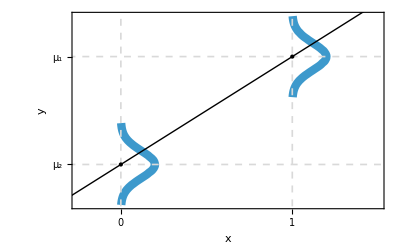

```mathematica
Block[{x1=2,μ1=10,x2=0,μ2=2,g1,g2,g},
g1=ContourPlot[x-x1==PDF[NormalDistribution[μ1,1],y],{x,x2-0.5,x1+1},{y,μ2-3,μ1+3},
PlotTheme->"LargeLabels",PlotPoints->20,ContourStyle->Thickness[0.015],
RegionFunction->Function[{x,y},μ1-3<y<μ1+3]];
g2=ContourPlot[x-x2==PDF[NormalDistribution[μ2,1],y],{x,x2-0.5,x1+1},{y,μ2-3,μ1+3},
PlotPoints->20,ContourStyle->Thickness[0.015],
RegionFunction->Function[{x,y},μ2-3<y<μ2+3]];
g=Show[g1,g2,
Background->None,
AspectRatio->1/GoldenRatio,
FrameLabel->{x,y},
FrameTicks->{{{{μ2,"μ_2"},{μ1,"μ_1"}},None}, {{{x2,0},{x1,1}},None}},
GridLines->{{x2,x1}, {μ2,μ1}},GridLinesStyle->Directive[Dashed,Thickness[0.003]],
Epilog->{Thick,PointSize[Large],InfiniteLine[{{x2,μ2},{x1,μ1}}],Point[{{x2,μ2},{x1,μ1}}]}];
Print[g];
SetOptions[$FrontEnd,LightDark->"Dark"];
Export[FileNameJoin[DIR,"ex34-dark.svg"],g,Background->None];
SetOptions[$FrontEnd,LightDark->"Light"];
Export[FileNameJoin[DIR,"ex34-light.svg"],g,Background->None];
SetOptions[$FrontEnd,LightDark->Automatic]
]
```

## Ex 10.38

```mathematica
SolveValues[(Subscript[β̂, 0]+Subscript[β̂, 1] Subscript[x, 0]-Subscript[μ, 0])^2/(s^2(1/n+(Subscript[x, 0]- x̄)^2))==t^2,Subscript[x, 0]]
```

{1/(2 (-n s^2 t^2+n (β̂)_1^2))(-2 n s^2 t^2 x̄+2 n μ_0 (β̂)_1-2 n (β̂)_0 (β̂)_1-√((2 n s^2 t^2 x̄-2 n μ_0 (β̂)_1+2 n (β̂)_0 (β̂)_1)^2-4 (-s^2 t^2-n s^2 t^2 (x̄)^2+n μ_0^2-2 n μ_0 (β̂)_0+n (β̂)_0^2) (-n s^2 t^2+n (β̂)_1^2))),1/(2 (-n s^2 t^2+n (β̂)_1^2))(-2 n s^2 t^2 x̄+2 n μ_0 (β̂)_1-2 n (β̂)_0 (β̂)_1+√((2 n s^2 t^2 x̄-2 n μ_0 (β̂)_1+2 n (β̂)_0 (β̂)_1)^2-4 (-s^2 t^2-n s^2 t^2 (x̄)^2+n μ_0^2-2 n μ_0 (β̂)_0+n (β̂)_0^2) (-n s^2 t^2+n (β̂)_1^2)))}

```mathematica
FullSimplify[SolveValues[(Subscript[β̂, 0]+Subscript[β̂, 1] Subscript[x, 0]-Subscript[μ, 0])^2/(s^2(1/n+(Subscript[x, 0]- x̄)^2/sxx))==t^2,Subscript[x, 0]],Subscript[β̂, 1]^2<(t^2 s^2)/sxx∧s>0∧t>0]
```

{(n s^2 t^2 x̄+n sxx (-μ_0+(β̂)_0) (β̂)_1+s t √(n sxx (-s^2 t^2+n (μ_0-(β̂)_0)^2+2 n x̄ (-μ_0+(β̂)_0) (β̂)_1+(sxx+n (x̄)^2) (β̂)_1^2)))/(n (s^2 t^2-sxx (β̂)_1^2)),(n s^2 t^2 x̄+n sxx (-μ_0+(β̂)_0) (β̂)_1-s t √(n sxx (-s^2 t^2+n (μ_0-(β̂)_0)^2+2 n x̄ (-μ_0+(β̂)_0) (β̂)_1+(sxx+n (x̄)^2) (β̂)_1^2)))/(n (s^2 t^2-sxx (β̂)_1^2))}

```mathematica
Inequality
```

\bar{x}